# Broadband Network Congestion Measurement - ICMP ping measurements

How long as TWC been aware of network congestion in High Speed Internet service to Hana, HI?

by Chase.Turner@TFarms.com

For discussion purposes only.  Use of this report requires specific permission of the author.

## Terminology

## Sources

### Display and Legends

#### City where probe is located

```mathematica
ClearAll[cityOfProbe];
Block[{},
cityOfProbe[1165]="Maui:Hana";
cityOfProbe[1178]="Maui:Hana";
cityOfProbe[15111]="Maui:Kahului";
cityOfProbe[2289]="BI:Hawi";
cityOfProbe[12735]="BI:Kailua-Kona";
cityOfProbe[10546]="BI:Hilo";
cityOfProbe[14720]="Oahu:Kaneohe";
];
(* TEST *)
cityOfProbe/@ allProbes
```

allProbes

#### Color Scheme for probes

```mathematica
allProbes={1178,1165,15111,2289,12735,10546,14720};
```

```mathematica
ClearAll[colorCodeForProbe];
Block[{},
colorCodeForProbe[1165]=Blue;
colorCodeForProbe[1178]=Red;
colorCodeForProbe[15111]=Purple;
colorCodeForProbe[2289]=Gray;
colorCodeForProbe[12735]=Orange;
colorCodeForProbe[10546]=LightPink;
colorCodeForProbe[14720]=Black;
];
```

#### PlotStyle for probe

```mathematica
ClearAll[plotStyleForProbe];
plotStyleForProbe[aProbe_Integer, pSize_, pOpacity_]:=colorCodeForProbe[aProbe];
(* TEST *)
plotStyleForProbe[#,.001,0.5]&/@ allProbes
```

{RGBColor[1,0,0],RGBColor[0,0,1],RGBColor[0.5,0,0.5],GrayLevel[0.5],RGBColor[1,0.5,0],RGBColor[1,0.925,0.925],GrayLevel[0]}

#### Pretty Print for Probe

```mathematica
ClearAll[pprintProbe];
pprintProbe[probe_Integer]:= Style["p"<>ToString[probe] <> "_"<>cityOfProbe[probe],FontColor->colorCodeForProbe[probe], Plain,"Text"];
(* TEST *)
pprintProbe/@ allProbes
```

{p1178_Maui:Hana,p1165_Maui:Hana,p15111_Maui:Kahului,p2289_BI:Hawi,p12735_BI:Kailua-Kona,p10546_BI:Hilo,p14720_Oahu:Kaneohe}

### Sources

```mathematica
pingMeasurements={
{1604357,"pingToChase"},
{1604419,"pingNetflix"},
{1664935,"ping-72.129.45.3-transpacific"},
{1664936,"ping-72.129.45.55"},
{1664937,"ping-72.129.45.79"},
{1665597,"ping-24.25.227.55"},
{1665886,"ping-24.94.68.1"},
{1607723,"ping-24.25.230.138-GE17-0"},
{1665888,"ping-24.25.230.137-GE18-0"}
};
```

#### fetchJSONMeasurement

```mathematica
ClearAll[fetchJSONMeasurement];
Needs["JLink`"];
fetchJSONMeasurement[resultNumber_Integer, friendlyName_String]:=Module[
{defaultCacheDir, fullPathToCache,uri, jsonData},
defaultCacheDir=FileNameJoin[{NotebookDirectory[], "data"}];
fullPathToCache=FileNameJoin[{defaultCacheDir,"RIPE-Atlas-measurement-"<>ToString[resultNumber]<>"-"<>friendlyName<>".json"}];
uri="https://atlas.ripe.net/api/v1/measurement/"<>ToString[resultNumber]<>"/result";

(* PREPARE JSON PARSER FOR LARGE FILES  *)
InstallJava[];
ReinstallJava[CommandLine->"java",JVMArguments->"-Xmx2024m"];

If[FileExistsQ[fullPathToCache],
jsonData=Import[fullPathToCache,"JSON"],
Module[{},
jsonData=Import[uri,"JSON"];
Export[fullPathToCache,jsonData,"JSON"]];
(* CLEAN UP JSON PARSER *)
UninstallJava[];
(* --->RETURNING *)
jsonData
]
];

(* TEST *)
If[False,fetchJSONMeasurement/@ pingMeasurements,Message["Test skipped; did not load JSON files"]];
```

Message::name: Message name "Test skipped; did not load JSON files" is not of the form symbol::name or symbol::name::language.

### Selected Data

```mathematica
(* tPingData *)
ClearAll[tPingData];
tPingData::usage="Organize entires here to reflect traceroute path";
```

```mathematica
tPingData=Flatten[fetchJSONMeasurement[#[[1]],#[[2]]]&/@{
(* Egress Path *)
{1665886,"ping-24.94.68.1-egress-hop1"},
{1665888,"ping-24.25.230.137-egress-hop2"},
(* transpacific entry point *)
{1664935,"ping-72.129.45.3-transpacific"},
(* Ingress Path *)
{1607723,"ping-24.25.230.138-ingress-hop1"},
{1664937,"ping-72.129.45.79-ingress-hop2"},
{1664936,"ping-72.129.45.55-ingress-hop3"},
(* DNS *)
{1665597,"ping-24.25.227.55-DNS"},
(* Netflix in CA *)
{1604419,"ping-65.19.157.233-Netflix"},
(* ping to Chase *)
{1604419,"ping-24.94.68.214-HanaHouse"}
},1];
(* TEST *)
{Dimensions[#,Depth[#]], Depth[#],LeafCount[#]}&/@ {tPingData}
```

{{{543702},7,49208739}}

### Transcode

#### Conversion of Unix Machine Timestamp to MathematicaTime

```mathematica
ClearAll[unixTimeToHST];
unixTimeToHST::usage="Given a atlas.ripe.net timestamp, convert to Unix time and adjuat to HST";
(* MESSAGES *)
unixTimeToHST::unexpectedArgument["`1`"];
(* IMPLEMETATION *)
(* Hawaiian Timezone is -10 from GMT *)
unixTimeToHST[x_Integer]:=DateList[AbsoluteTime[{1970,1,1,2,0,0}]+x,TimeZone->-10.0];
(* UNEXPECTED ARGUMENTS *)
unixTimeToHST[x_]:=Message[unixTimeToHST::unexpectedArgument,x];
(* TEST *)
unixTimeToHST[1330434000]
{2012,2,28,10,0,0.}
```

{2012,2,28,10,0,0.}

{2012,2,28,10,0,0.}

#### Verify : result types are known

Purpose of this section is to verify result types and values are known -- by a process of elimination.

Strategy: Collect results, and then specify patterns and delete.  The result should be an empty set.

```mathematica
ClearAll[results];
results::usage="Holds timing results";
results::unknownPattern="An unknown pattern was detected";
results::patternsVerified="All results matched known patterns";
results="result"/. tPingData;
```

```mathematica
ClearAll[pNormal,pDup1,pDup2,pUnreachable,pUnreachable2,pAllPatterns];
pNormal={"rtt"->rtt_}|{"rtt"->rtt_,"ttl"->_Integer};
pDup1={"dup"->_Integer,"rtt"->rtt_};
pDup2={"dup"->_Integer,"rtt"->rtt_,"ttl"->_Integer};
pUnreachable={"srcaddr"->ipAddr_String, "x"->"*"};
pUnreachable2={"x"->"*"};
pAllPatterns={pNormal,pDup1,pDup2,pUnreachable,pUnreachable2};
(* VERIFY *)
Block[{resultsWithUnknownValues},
resultsWithUnknownValues=DeleteCases[DeleteCases[#,Alternatives@@pAllPatterns]&/@results,{}];
If[Length[resultsWithUnknownValues]>0,
Message[results::unknownPattern], 
results::patternsVerified]]
```

results::unknownPattern: An unknown pattern was detected

#### Transcode JSON data to CDF

```mathematica
ClearAll[resultsToCDF];
(* MESSAGES *)
resultsToCDF::usage="Convert the JSON data into CDF Array";
resultsToCDF::unexpectedArg="`1`";

(* IMPLEMENTATION *)
resultsToCDF[aJSONResults_List]:= Block[{rtts, dropped},
rtts="rtt"/. Cases[aJSONResults,pNormal];
(* FIXME - what should be done with the DUP matches?  At present, they are ignored *)
dropped=Cases[aJSONResults,pUnreachable|pUnreachable2];
(* ---> RETURNING *)
{rtts,dropped}
];
(* UNEXPECTED ARGUMENT *)
resultsToCDF[x_]:=Message[resultsToCDF::unexpectedArg,x];

ClearAll[jsonToCDF];
(* MESSAGES *)
jsonToCDF::usage="Convert the JSON data into CDF Array";
jsonToCDF::unexpectedArg="`1`";

(* IMPLEMENTATION *)
jsonToCDF[aJSON_List]:= Block[{convertedData},
convertedData={"prb_id","dst_addr","sent","timestamp","result"}/.#&/@aJSON;
Join[#[[1;;3]],{unixTimeToHST[#[[4]]]},resultsToCDF[#[[5]]]]&/@ convertedData
];

jsonToCDF[aResult_String]={{},0};

(* UNEXPECTED ARGUMENT *)
jsonToCDF[x_]:=Message[jsonToCDF::unexpectedArg,x];

(* TEST *)
Length[tPingDataCDF=jsonToCDF[tPingData]]
```

543702

#### Result Summary Types

```mathematica
rttMean::usage="Mean value";
rttMean5pct::usage="Mean of RTTs after dropping 5% of smallest and largest elements";
rttMean95pct::usage="Mean of RTTs after dropping 95% of smallest and largest elements";
rttMax::usage="Maximum RTT value from the set";
rttMin::usage="Minimum RTT value from the set";
rttMean[rtt_List]:=Mean[rtt];
rttMean95pct[rtt_List]:=TrimmedMean[rtt,0.05];
rttMean5pct[rtt_List]:=TrimmedMean[rtt,0.45];
rttMax[rtt_List]:=Max[rtt];
rttMin[rtt_List]:=Min[rtt];
```

#### Accessor Functions

```mathematica
ClearAll[targetsIn];

targetsIn[tData_List]:=
DeleteDuplicates[Cases[tData,{
prbID_Integer,
target_String,
sent_Integer,
timestamp_,
rttList_List,
dropped_List
}:>target]
];
(* TEST *) 
targetsIn[tPingDataCDF]
```

{198.45.56.12,24.25.230.138,72.129.45.3,72.129.45.55,72.129.45.79,24.25.227.55,24.94.68.1,24.25.230.137}

```mathematica
probesIn[tData_List]:=
DeleteDuplicates[Cases[tData,{
prbID_Integer,
target_String,
sent_Integer,
timestamp_,
rttList_List,
dropped_List
}:>prbID]
];
(* TEST *) 
probesIn[tPingDataCDF]
```

{1178,15111,10546,1165,12735,14720,2289}

```mathematica
ClearAll[selectByHours];

selectBy[tData_List,probes_List,targetIP_String]:=Cases[tData,
{
prbID_Integer,
target_String,
sent_Integer,
timestamp_,
rttList_List,
dropped_List
}/; And[
MemberQ[probes,prbID] , 
StringMatchQ[target,targetIP]]
];
(* TEST *)
Length[selectBy[tPingDataCDF,{1165},"24.94.68.1"]]
```

4654

```mathematica
ClearAll[selectByHours];

selectByHours[tData_List,probes_List,targetIP_String,hours_List]:=Cases[tData,
{
prbID_Integer,
target_String,
sent_Integer,
timestamp_,
rttList_List,
dropped_List
}/; And[
MemberQ[probes,prbID] , 
StringMatchQ[target,targetIP],
MemberQ[hours,timestamp[[4]]]]
];
(* TEST *)
Length[selectByHours[tPingDataCDF,{1165},"24.94.68.1",{1}]]
```

195

```mathematica
Clear[selectByTimeSlice];

selectByTimeSlice[tData_List,probes_List,targetIP_String,timeSlice_List]:=Cases[tData,
{
prbID_Integer,
target_String,
sent_Integer,
timestamp_,
rttList_List,
dropped_List
}/; And[
MemberQ[probes,prbID] , 
StringMatchQ[target,targetIP],
AbsoluteTime[timeSlice[[1]]]≤ AbsoluteTime[timestamp] ≤AbsoluteTime[timeSlice[[2]]]
]
];
(* TEST *)
Length[selectByTimeSlice[tPingDataCDF,{1165},"24.94.68.1",{{2014,5,19,11},{2014,5,19,12}}]]
```

15

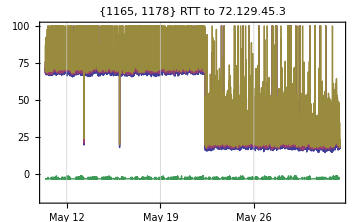
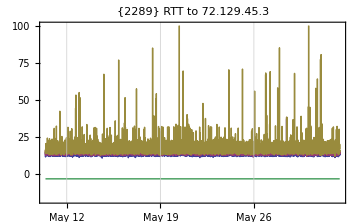
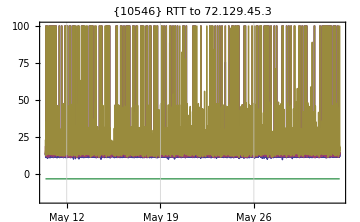
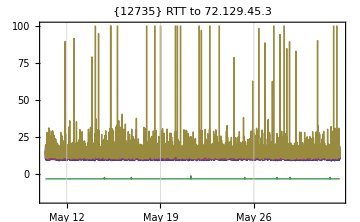
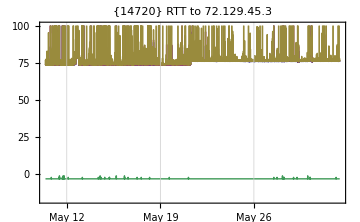
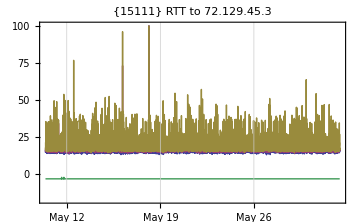

```mathematica
ClearAll[rttDateListPlot];

rttDateListPlot[tData_List,probes_List,targetIP_String]:=
Block[{matches,timeAndRtt,timeAndDropCount},
matches=selectBy[tData,probes,targetIP];
timeAndRtt=
{
{#[[4]],rttMin[#[[5]]]}&/@matches,
{#[[4]],rttMean5pct[#[[5]]]}&/@matches,
{#[[4]],rttMax[#[[5]]]}&/@matches,
{#[[4]],-Length[#[[5]]]}&/@matches
}
;

DateListPlot[
timeAndRtt,
PlotRange->{Automatic,{-17, 100}},
Joined->True,
ImageSize->Small,
PlotLabel->ToString[probes]<> " RTT to "<>targetIP
]
];

(* TEST *)
Table[rttDateListPlot[tPingDataCDF,probe,"72.129.45.3"],{probe, {1165},{1178}}]
```

## Egress

```mathematica
(* Egress Path *)
{1665886,"ping-24.94.68.1-egress-hop1"},
{1665888,"ping-24.25.230.137-egress-hop2"},
(* transpacific entry point *)
{1664935,"ping-72.129.45.3-transpacific"},
(* Ingress Path *)
{1607723,"ping-24.25.230.138-ingress-hop1"},
{1664937,"ping-72.129.45.79-ingress-hop2"},
{1664936,"ping-72.129.45.55-ingress-hop3"},
(* DNS *)
{1665597,"ping-24.25.227.55-DNS"},
(* Netflix in CA *)
{1604419,"ping-65.19.157.233-Netflix"},
(* ping to Chase *)
{1604419,"ping-24.94.68.214-HanaHouse"}
Table[rttDateListPlot[tPingDataCDF,probe,"24.94.68.1"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}]
```

### 24.94.68.1 - 1st Hop out for Hana

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"24.94.68.1"],{probe, {1165,1178}}]
```

### 24.25.230.137 - 2nd Hop out for Hana

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"24.25.230.137"],{probe, {1165,1178}}]
```

### 72.129.45.3 - Transpacific Entry Point

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"72.129.45.3"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}]
```

### 65.19.157.233 - Netflix

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"65.19.157.233"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}]
```

## Ingress

### 24.25.230.138 - Last hop before landing at Hana

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"24.25.230.138"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}]
```

### 72.129.45.79 - 2nd to Last Hop before landing at Hana

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"72.129.45.79"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}]
```

### 72.129.45.55 - Hop delivering to Hana and Kehei

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"72.129.45.55"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}]
```

### 24.94.68.214 - Ping Chase’s house

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"72.129.45.55"],{probe, {{1165},{15111},{2289},{10546},{12735},{14720}}}]
```

## DNS

### 24.25.227.55 - DNS

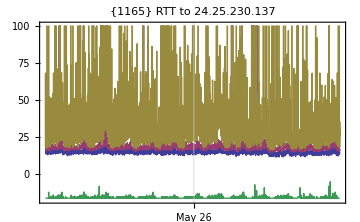
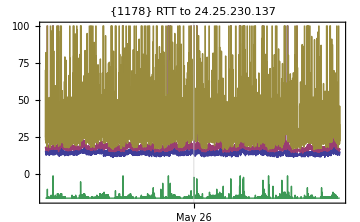

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"24.25.227.55"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}]
```

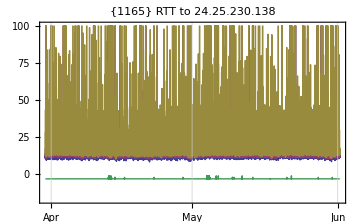
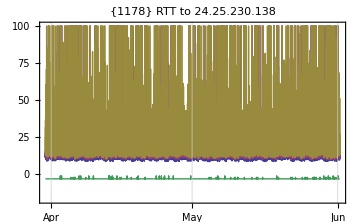

```mathematica
Table[rttDateListPlot[tPingDataCDF,{probe},"24.25.230.138"], {probe, {1165,1178}}]
```

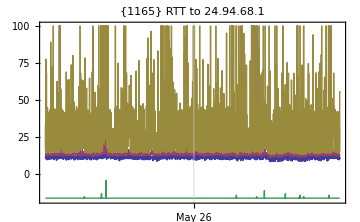
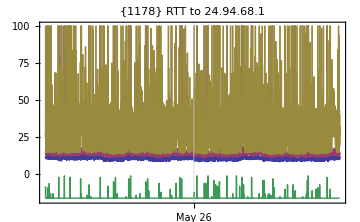

```mathematica
Table[rttDateListPlot[tPingDataCDF,{probe},"24.94.68.1"], {probe, {1165,1178}}]
```

```mathematica
Sort[probesIn[tPingDataCDF]]
```

{1165,1178,2289,10546,12735,14720,15111}

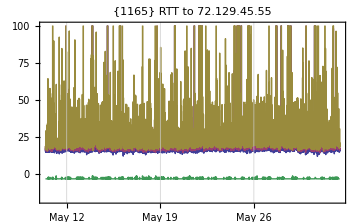
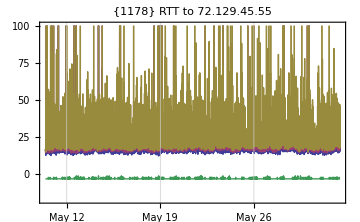

```mathematica
Table[rttDateListPlot[tPingDataCDF,{probe},"72.129.45.55"], {probe, {1165,1178}}]
```

## SCRATCH